```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/henryzheng/Documents/PhD_work/Integer_powers/Integer_powers

Steps to produce results:
1. Generate linear powerspectrum (from CLASS)
2. Fit Linear power spectrum with IntegerFit
3. Construct kernel for diagram
4. Decompose kernel into tabs of exponents of q^2, k1mq^2 ,k2pq^2 and coefficients
5. Export tabs and evaluate with J function
6. Import tensor output from python and contract with power spectrum fitting coefficients

## Preliminaries

Import Linear Power Spectrum

```mathematica
plinnum = "42";
```

```mathematica
norm = Import["pk_fid.dat"][[All,2]]//Max;
norm2 = Import["pk_for_Henry/pk_"<>plinnum<>".dat"][[All,2]]//Max;
```

```mathematica
plin= Interpolation[Import["pk_fid.dat"]];
```

```mathematica
plinTest[q_] = Interpolation[Import["pk_for_Henry/pk_"<>plinnum<>".dat"]][q]norm/norm2;
```

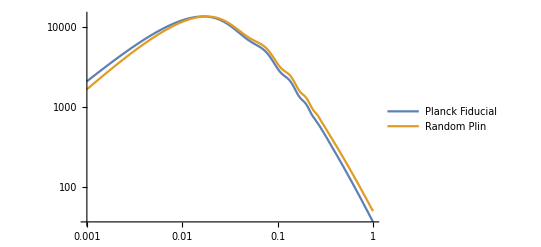

```mathematica
LogLogPlot[{plin[q],plinTest[q]},{q,10^-3,1}, PlotLegends->{"Planck Fiducial", "Random Plin"}]
```

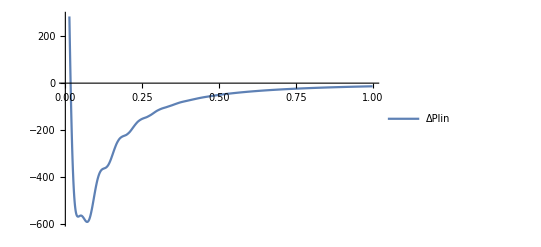

```mathematica
Plot[{plin[q]-plinTest[q]},{q,10^-3,1}, PlotLegends->{"ΔPlin"}]
```

### General Perturbation Theory Kernels

```mathematica
perm12=Permutations[{q1,q2}];
perm123=Permutations[{q1,q2,q3}];
perm1234=Permutations[{q1,q2,q3,q4}];
```

```mathematica
Clear[Fn,Gn,n,m,k1,k2,k3];
Fn[n_,v_]:=Fn[n,v]=If[n==1,1,Sum[(Gn[m,v[[1;;m]]]/((2n+3)(n-1)))((2n+1)al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
Gn[n_,v_]:=Gn[n,v]=If[n==1,1,Sum[(Gn[m,v[[1;;m]]]/((2n+3)(n-1)))(3al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2n be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
```

```mathematica
F2s[q1_,q2_]=Simplify[Sum[1/Length[perm12]Fn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
F3s[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123]Fn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
```

```mathematica
F4s[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234]Fn[4,{perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]}],{i,1,Length[perm1234]}]];
```

```mathematica
alf[k1_,k2_]=(k1+k2).k1/(k1.k1);
bef[k1_,k2_]=(k1+k2).(k1+k2)(k1.k2)/2/(k1.k1)/(k2.k2) ;
alfm[k1_,k2_]=1+(1/2)((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)/mag[k1]^2);
befm[k1_,k2_]=(mag[k1+k2]^2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2);
sigma2[k1_,k2_]=(1/4)((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)^2/(mag[k1]^2 mag[k2]^2))-1;
```

```mathematica
Gal3[k1_,k2_,k3_]:=((-1)/2)(1-3((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)^2/(4 mag[k1]^2 mag[k2]^2))+ ((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)(mag[k1+k3]^2-mag[k1]^2-mag[k3]^2)(mag[k3+k2]^2-mag[k3]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2 mag[k3]^2));
```

## Fit Linear Power Spectrum

### Functions for fitting

```mathematica
kBinslin[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=(kmax-kmin)/(Nmax-1)//N;
result=Table[kmin +(i-1) Δ,{i,1,Nmax}];
result
];
```

```mathematica
(* Nmax log k bins, from kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=(1/(Nmax-1))Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
NmaxPlot=100;
NmaxFit=100;
kminPlot=10^-3;
kminFit=10^-3;
kmaxPlot=2.;
kmaxFit=0.6;
knPlot=kBins[NmaxPlot,kminPlot,kmaxPlot];
knFit=kBins[NmaxFit,kminFit,kmaxFit];
knFitlin=kBinslin[NmaxPlot,kminPlot,kmaxFit];
```

Function for fitting linear power spectrum: knFit are the k’s to fit generated by kBinslin

```mathematica
IntegerFit[Plin_,knFit_,imax_]:=Module[{MyPsmoothtab,MyFitFunctions,Parameters,nlm,Pinteger,errors,kuv0,kuv1,kuv2,kuv3,kuv4,kpeak1,kpeak2,kpeak3,kpeak4},
MyPsmoothtab = Table[{knFit⟦i⟧,Plin[knFit⟦i⟧]},{i,1,Length[knFit]}];
errors=Flatten[Table[{MyPsmoothtab⟦i,2⟧ 10^-6},{i,1,Length[knFit]}]];

kuv0 = 0.0001;
kuv1=0.069;
kuv2=0.0082;
kuv3=0.0013;
kuv4=0.0000135;
kpeak1=-0.034;
kpeak2=-0.001;
kpeak3=-0.000076;
kpeak4=-0.0000156;

Parameters=Flatten[Table[{a1[i],a2[i],a3[i],a4[i]},{i,0,imax}]];
MyFitFunctions=Delete[Flatten[Join[{1/(1+k^2/kuv0)},Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k/(1/20))^2/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)),1/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)),1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]]],2];

nlm=LinearModelFit[MyPsmoothtab,MyFitFunctions,k,Weights->1/errors^2,IncludeConstantBasis->False]; 
Pinteger[k_]=nlm[k];
{Pinteger,nlm["BestFitParameters"]}
]
imax=3;
{Pinteger,coeflin}=IntegerFit[plin,knFit,imax];
```

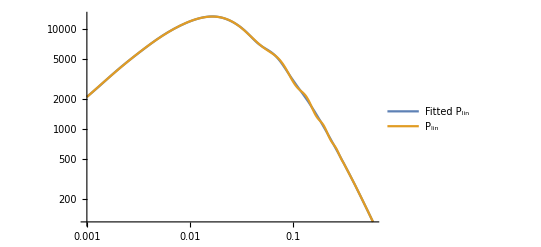

```mathematica
LogLogPlot[{Pinteger[q],plin[q]},{q,0.001,0.6},PlotLegends->{"Fitted P_lin", "P_lin"}]
```

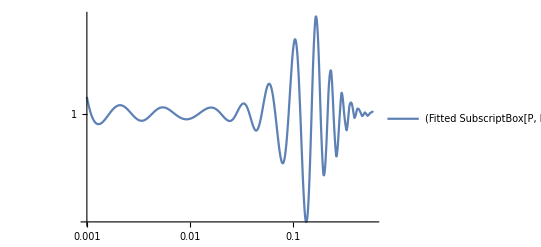

```mathematica
LogLogPlot[{Pinteger[q]/plin[q]},{q,0.001,0.6},PlotLegends->{"(Fitted SubscriptBox[P, lin])/P_lin"},PlotRange->All]
```

```mathematica
ΔPlin[q_]=plinTest[q]-plin[q];
```

```mathematica
{ΔPinteger,coeflin}=IntegerFit[ΔPlin,knFit,imax+2];
```

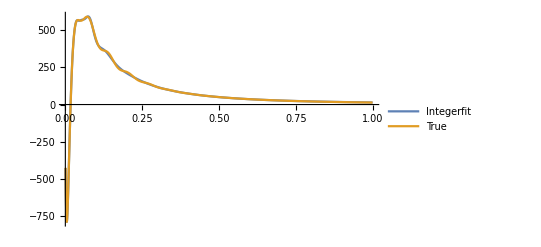

```mathematica
Plot[{ΔPinteger[q], ΔPlin[q]}, {q,10^-3,1}, PlotLegends->{"Integerfit", "True"},PlotRange->All]
```

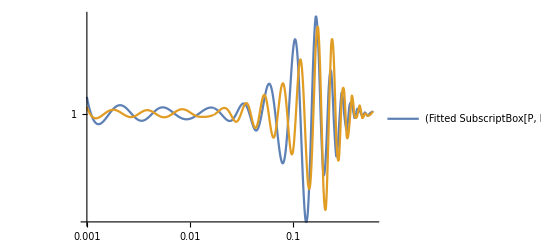

```mathematica
LogLogPlot[{{Pinteger[q]/plin[q],ΔPinteger[q] /ΔPlin[q]}},{q,0.001,0.6},PlotLegends->{"(Fitted SubscriptBox[P, lin])/P_lin"},PlotRange->All]
```

## One Loop Power Spectrum Example: P22

Generate kernel for P22

```mathematica
ker22 = (2F2s[q,k-q]F2s[q,k-q]/.{al->alfm,be->befm}/.mag[-q]->mag[q]/.{mag[q]->q,mag[k]->k,mag[-k]->k,mag[k1+k2]->k3,mag[k-q]->kmq,mag[k+q]->kpq}//Expand);
```

Decompose into tabs of exponents

```mathematica
ker22list=(List@@ker22);
Tab22[k_] = Table[{Exponent[ker22list⟦i⟧,q^2],Exponent[ker22list⟦i⟧,kmq^2],ker22list⟦i⟧/.{q-> 1,kmq-> 1}},{i,1,Length[ker22list]}];
CTab22full[k_]=Sort[Tab22[k]];
```

Export tab for python evaluation

```mathematica
genP22ctab[k_]:=Export["3. Ctabs/P22ctabks/P22ctab_"<>ToString[k//N]<>"_.csv",N[CTab22full[k],50],"Table"];
```

Produce tab example: k = 0.1

```mathematica
genP22ctab[0.1]
```

3. Ctabs/P22ctabks/P22ctab_0.1_.csv

Run “python P22_jfunc_cython_v1.py” to produce output “P22ctab_0.1_.csv” in folder “3. Ctabs/P22ctabks”

Import python output “2. Jmat_loopvals/P22_Jmat_cython/P22_Jfunc_0.1_.csv”

```mathematica
P22k0p1 = Import["2. Jmat_loopvals/P22_Jmat_cython/P22_Jfunc_0.1_.csv"];
```

Python out is a 16 by 16 matrix indexed by position of fitting function

```mathematica
P22k0p1//Dimensions
```

{16,16}

Contract with fitting coefficients

```mathematica
P22ana = coeflin.P22k0p1.coeflin
```

473.798

### Numerical integration bounds and parameters

```mathematica
qir=0.0000001;(*qir=0.00005;*) quv=10;
subsp1loop={kmq->√(k^2+q^2-2 k q ν),kpq->√(k^2+q^2+2 k q ν)};
```

### Comparison to Numerical Integration

```mathematica
P22num = NIntegrate[q^2/(2π)^3 ker22 Pinteger[q]Pinteger[kmq]/.subsp1loop/.k-> 0.1,{ν,-1,1},{q,qir, quv},{ϕ,0,2π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

473.798

```mathematica
NIntegrate[q^2/(2π)^3 ker22 plinTest[q]plinTest[kmq]norm2^2/norm^2/.subsp1loop/.k-> 0.1,{ν,-1,1},{q,qir, quv},{ϕ,0,2π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1120.19

```mathematica
base = NIntegrate[q^2/(2π)^3 ker22 plin[q]plin[kmq]/.subsp1loop/.k-> 0.1,{ν,-1,1},{q,qir, quv},{ϕ,0,2π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

474.94

```mathematica
res=base + NIntegrate[q^2/(2π)^3 ker22 (ΔPlin[q])(plin[kmq])/.subsp1loop/.k-> 0.1,{ν,-1,1},{q,qir, quv},{ϕ,0,2π},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]+ NIntegrate[q^2/(2π)^3 ker22 (plin[q])(ΔPlin[kmq])/.subsp1loop/.k-> 0.1,{ν,-1,1},{q,qir, quv},{ϕ,0,2π},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}](*+NIntegrate[q^2/(2π)^3 ker22 (ΔPlin[q])(ΔPlin[kmq])/.subsp1loop/.k-> 0.1,{ν,-1,1},{q,qir, quv},{ϕ,0,2π},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

557.083

```mathematica
1-norm2^2/norm^2 res/1120.187777616849
```

0.00448587

```mathematica
P22ana/P22num
```

1.

## One Loop Bispectrum Example: B222

### Construct Kernel

```mathematica
ker222[k1_,k2_,k3_]=(((8F2s[q,-q+k1]F2s[-q+k1,q+k2]F2s[k2+q,-q]/.{al->alfm,be->befm})/.mag[-q]->mag[q])/.{mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k1+k2]->k3,mag[k1-q]->k1mq,mag[k2+q]->k2pq})//Expand;
```

### Decompose Kernel and generate tabs

```mathematica
ker222list[k1_,k2_,k3_]:= List@@ker222[k1,k2,k3];
```

```mathematica
B222ctab[k1_,k2_,k3_] = Table[{Exponent[ker222list[k1,k2,k3]⟦i⟧,q^2],Exponent[ker222list[k1,k2,k3]⟦i⟧,k1mq^2],Exponent[ker222list[k1,k2,k3]⟦i⟧,k2pq^2],ker222list[k1,k2,k3]⟦i⟧/.{q-> 1,k1mq-> 1,k2pq-> 1}},{i,1,Length[ker222list[k1,k2,k3]]}];
```

```mathematica
B222ctabreduc[k1_,k2_,k3_]=Sort[B222ctab[k1,k2,k3]//.{a___,{p_,q_,r_,s1_},b___,{p_,q_,r_,s2_},c___}:>{a,{p,q,r,s1+s2},b,c}];
```

```mathematica
genb222ctab[k1_,k2_,k3_]:=Export["3. Ctabs/B222ctabks/B222ctab_"<>ToString[k1//N]<>"_"<>ToString[k2//N]<>"_"<>ToString[k3//N]<>"_.csv",N[B222ctabreduc[Rationalize[k1],Rationalize[k2],Rationalize[k3]],80],"Table"];
```

Produce ctab example for k1 = 0.1, k2 = 0.15, k3 = 0.2 for python input.

```mathematica
genb222ctab[0.1,0.15,0.2]
```

3. Ctabs/B222ctabks/B222ctab_0.1_0.15_0.2_.csv

Run “python B222_jfunc_cython_v1.py” to produce output 
“2. Jmat_loopvals/B222_Jmat_cython/B222_Jfunc_0.1_0.15_0.2_.h5”

### Import from Python

Import python output “2. Jmat_loopvals/B222_Jmat_cython/B222_Jfunc_0.1_0.15_0.2_.h5”

```mathematica
B222ex = Import["2. Jmat_loopvals/B222_Jmat_cython/B222_Jfunc_0.1_0.15_0.2_.h5","jmat"];
```

Python out is a 16x16x16 matrix indexed by position of fitting function

```mathematica
B222ex//Dimensions
```

{16,16,16}

Contract with fitting coefficients

```mathematica
B222ana = coeflin.B222ex.coeflin.coeflin
```

460009.

### Numerical integration bounds and parameters

```mathematica
(*qir=0.0001;*)qir=0.00005; quv=1;
```

```mathematica
keval = {0.17,0.17,0.17};
```

```mathematica
Clear[k1vec,k2vec,qvec,k1,k2,k3,ϕs,q]
k1vec=k1{0,0,1};
ν2= (k3^2-k2^2-k1^2)/(2k1 k2);
k2vec=k2{0,√(1-ν2^2),ν2};
k3vec=-k1vec-k2vec;

qvec=q{Cos[ϕs] √(1-ν^2),Sin[ϕs] √(1-ν^2),ν};
k1mqvec=k1vec-qvec//Simplify;
k2pqvec=k2vec+qvec//Simplify;
k1pqvec=k1vec+qvec//Simplify;
k2mqvec=k2vec-qvec//Simplify;
k3pqvec=k3vec+qvec//Simplify;
k3mqvec=k3vec-qvec//Simplify;
```

```mathematica
subs={k1mq->√(k1mqvec.k1mqvec),k2pq->√(k2pqvec.k2pqvec),k1pq->√(k1pqvec.k1pqvec),k2mq->√(k2mqvec.k2mqvec),k3pq-> (k3pqvec.k3pqvec)^(1/2),k3mq-> (k3mqvec.k3mqvec)^(1/2)}//Simplify;
subsp1loop={kmq-> √(q^2+k^2-2 k q ν),kpq-> √(q^2+k^2+2 k q ν)};
```

```mathematica
magreps ={mag[0]-> 0,mag[-q]->q,mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k3]->k3,mag[-k1]->k1,mag[-k2]->k2,mag[-k1-k2]->k3,mag[k1+k2]->k3,mag[-k1+q]->k1mq,mag[k1-q]->k1mq,mag[-k1-q]->k1pq,mag[k1+q]->k1pq,mag[-k2+q]->k2mq,mag[k2-q]->k2mq,mag[-k2-q]->k2pq,mag[k2+q]->k2pq,mag[-k1-k2-q]->k3mq,mag[k1+k2+q]->k3mq,mag[-k1-k2+q]->k3pq,mag[k1+k2-q]->k3pq,mag[-k3]->k3,mag[-k1-k3]->k2,mag[k1+k3]->k2,mag[-k3+q]->k3mq,mag[k3-q]->k3mq,mag[-k3-q]->k3pq,mag[k3+q]->k3pq,mag[-k1-k3-q]->k2mq,mag[k1+k3+q]->k2mq,mag[-k1-k3+q]->k2pq,mag[k1+k3-q]->k2pq,mag[-k2-k3]->k1,mag[k2+k3]->k1,mag[-k2-k3-q]->k1mq,mag[k2+k3+q]->k1mq,mag[-k2-k3+q]->k1pq,mag[k2+k3-q]->k1pq};
```

```mathematica
plinTestNoRescale= Interpolation[Import["pk_42.dat"]];
```

```mathematica
B222ker = ker222@@keval plinTestNoRescale[q]plinTestNoRescale[k1mq]plinTestNoRescale[k2pq]/.subs/.Thread[{k1,k2,k3}->keval];
```

```mathematica
truth = NIntegrate[q^2/(2π)^3 B222ker,{ν,-1,1},{ϕs,0,2π},{q,qir,quv},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

8.88809433×10^6

```mathematica
B222kerBase = ker222@@keval plin[q]plin[k1mq]plin[k2pq]/.subs/.Thread[{k1,k2,k3}-> keval];
B222kerp1 = ker222@@keval ΔPlin[q]plin[k1mq]plin[k2pq]/.subs/.Thread[{k1,k2,k3}-> keval];
B222kerp2 = ker222@@keval plin[q]ΔPlin[k1mq]plin[k2pq]/.subs/.Thread[{k1,k2,k3}-> keval];
B222kerp3 = ker222@@keval plin[q]plin[k1mq]ΔPlin[k2pq]/.subs/.Thread[{k1,k2,k3}-> keval];
```

```mathematica
base = NIntegrate[q^2/(2π)^3 B222kerBase,{ν,-1,1},{ϕs,0,2π},{q,qir,quv},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
p1 = NIntegrate[q^2/(2π)^3 B222kerp1,{ν,-1,1},{ϕs,0,2π},{q,qir,quv},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
p2=NIntegrate[q^2/(2π)^3 B222kerp2,{ν,-1,1},{ϕs,0,2π},{q,qir,quv},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
p3=NIntegrate[q^2/(2π)^3 B222kerp3,{ν,-1,1},{ϕs,0,2π},{q,qir,quv},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
1-norm2^3/norm^3(base + p1 + p2 + p3)/truth
norm2^3/norm^3{base, p1, p2, p3}
```

0.040409041

{5.97960998×10^6,849762.252,849778.279,849784.453}

```mathematica
B222kerpp1=ker222@@keval ΔPlin[q]ΔPlin[k1mq]plin[k2pq]/.subs/.Thread[{k1,k2,k3}-> keval];
B222kerpp2=ker222@@keval ΔPlin[q]plin[k1mq]ΔPlin[k2pq]/.subs/.Thread[{k1,k2,k3}-> keval];
B222kerpp3=ker222@@keval plin[q]ΔPlin[k1mq]ΔPlin[k2pq]/.subs/.Thread[{k1,k2,k3}-> keval];
```

```mathematica
pp1 = NIntegrate[q^2/(2π)^3 B222kerpp1,{ν,-1,1},{ϕs,0,2π},{q,qir,quv},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
pp2=NIntegrate[q^2/(2π)^3 B222kerpp2,{ν,-1,1},{ϕs,0,2π},{q,qir,quv},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
pp3=NIntegrate[q^2/(2π)^3 B222kerpp3,{ν,-1,1},{ϕs,0,2π},{q,qir,quv},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
1-norm2^3/norm^3(base + p1 + p2 + p3+pp1+pp2+pp3)/truth
```

0.00160534

```mathematica
B222kerppp = ker222@@keval ΔPlin[q]ΔPlin[k1mq]ΔPlin[k2pq]/.subs/.Thread[{k1,k2,k3}-> keval];
correction =norm2^3/norm^3 NIntegrate[q^2/(2π)^3 B222kerppp,{ν,-1,1},{ϕs,0,2π},{q,qir,quv},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

14270.5037

```mathematica
res=norm2^3/norm^3(base + p1 + p2 + p3+pp1+pp2+pp3)+correction
1-res/truth
correction/truth
```

8.88809643×10^6

-2.37×10^-7

0.00160557519

```mathematica
test = Import["B3212_Jfunc_0.012_0.0232_0.1561_.h5","jmat"];(* This uses my jfunc file*)
test2 = Import["B3212_Jfunc_0.012_0.0232_0.1561_2.h5","jmat"];(*This uses Guido's Jfunc file*)
```

```mathematica
test==test2
```

True

```mathematica
test = Import["B222_Jfunc_0.012_0.0232_0.1561_.h5","jmat"];(* This uses my jfunc file*)
test2 = Import["B222_Jfunc_0.012_0.0232_0.1561_2.h5","jmat"];(*This uses Guido's Jfunc file*)
```

```mathematica
test==test2
```

True